```mathematica
c[t_]:=CellularAutomaton[30,{{1},0},{t,{{0}}}]
```

```mathematica
Frecuencies=Function[{column},
unique=DeleteDuplicates[column];
frecuencies=Table[{unique[[i]],Count[column,unique[[i]]]},{i,1,Length[unique]}];
frecuencies
];
```

```mathematica
Density=Function[{column,divisor},
partitions=Partition[column,divisor];
density=Table[Count[partitions[[i]],1],{i,1,Length[partitions]}];
density
];
```

```mathematica
HistoricFrecuency=Function[{column,divisor,min,increment},
historic=Table[Frecuencies[Density[column[[1;;i]],divisor]],{i,min,Length[column],increment}];
Do[
historic[[i,All,2]]=Normalize[historic[[i,All,2]]];
,{i,1,Length[historic]}];
historic
];
```

```mathematica
HistoricPlot=Function[{column,divisor,min,increment},
d=HistoricFrecuency[column,divisor,min,increment];
Manipulate[
StackedListPlot[d[[i]],PlotRange->{{0,divisor},{0,1}},AspectRatio->1,Frame->True,PlotStyle->Red,Mesh->All],
{i,1,Length[d],1}]
];
```

```mathematica
column=c[1000000][[;;-2]];
```

```mathematica
divisor=5;
min=10000;
increment=4000-Mod[4000,divisor];
```

```mathematica
historic=HistoricFrecuency[column,divisor,min,increment];
```

```mathematica
maxY=Max[Flatten[historic[[All,All,2]]]];
minX=Min[Flatten[historic[[All,All,1]]]];
maxX=Max[Flatten[historic[[All,All,1]]]];

Manipulate[
StackedListPlot[historic[[i]],PlotRange->{{minX,maxX},{0,maxY}},AspectRatio->1,Frame->True,PlotStyle->Red,Mesh->All],
{i,1,Length[historic],1}]
```

```mathematica
means=Table[Mean[historic[[i,All,2]]//N],{i,1,Length[historic]}];
variance=Table[Variance[historic[[i,All,2]]//N],{i,1,Length[historic]}];
standardDeviation=Table[StandardDeviation[historic[[i,All,2]]//N],{i,1,Length[historic]}];
median=Table[Median[historic[[i,All,2]]//N],{i,1,Length[historic]}];
skewness=Table[Skewness[historic[[i,All,2]]//N],{i,1,Length[historic]}];
kurtosis=Table[Kurtosis[historic[[i,All,2]]//N],{i,1,Length[historic]}];
```

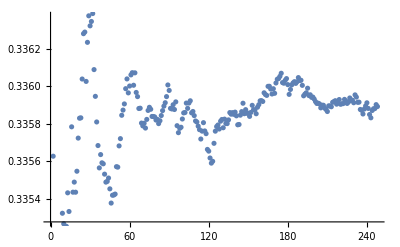

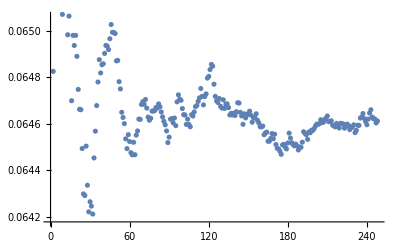

-Graphics-

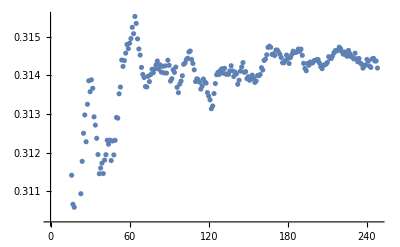

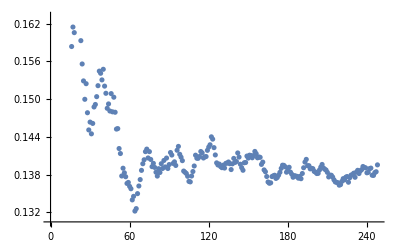

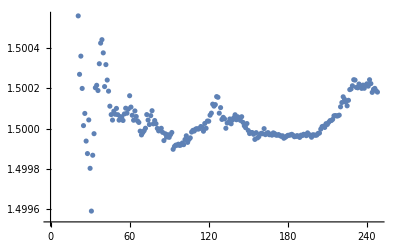

```mathematica
ListPlot[means]
ListPlot[variance]
ListPlot[means]
ListPlot[median]
ListPlot[skewness]
ListPlot[kurtosis]
```